```mathematica
searchlink="https://en.wikipedia.org/w/index.php?title=Special:Search&limit=500&offset=0&profile=default&search=computational&searchToken=b9fbzhit5sdhvvts5aa00u74l";
xmlResults=Import[searchlink, "XMLObject"];
articles=Union[Flatten[Cases[xmlResults,XMLElement[_,{_,_,
"title"->str_String/;
((StringMatchQ[str,StartOfString~~"Computational"~~__])&&!(StringContainsQ[str,"Journal",IgnoreCase->True])),_},_]->{str},Infinity]]];
```

```mathematica
{"article1","article2"}⇒ <|"article1"-> f["article1"],"article2"-> f["article1"]|>
```

```mathematica
TitleToInfo[articleTitle_String]:=AssociationMap[WikipediaData[articleTitle,#]&,{"ArticlePlaintext", "ExternalLinks","ArticleContributors", "PageID","SummaryPlaintext","LanguagesList","LinksList","BacklinksList"}];
```

```mathematica
compData=AssociationMap[TitleToInfo,articles];
```

```mathematica
cDataset = Dataset[compData];
ncDataset=Dataset[noncompData];
```

```mathematica
Thread[f[{a,b,...}]]={f[a],f[b],...}
```

```mathematica
Graph[Flatten@Map[Thread,Normal@Normal@cDataset[;;,"LinksList"]]]
```

-Graphics-

```mathematica
Flatten@Map[Thread,Normal@Normal@cDataset[;;,"LinksList"]]
```

{Computational aeroacoustics→Acoustic analogy,Computational aeroacoustics→Acoustic theory,Computational aeroacoustics→Aeroacoustics,Computational aeroacoustics→Boundary element method,Computational aeroacoustics→Computational Aeroacoustics,Computational aeroacoustics→Computational fluid dynamics,Computational aeroacoustics→Gustav Kirchhoff,6656,Computational X→Computational physics,Computational X→Computational thinking,Computational X→Computer science,Computational X→Geoffrey C. Fox,Computational X→Informatics,Computational X→Stephen Wolfram}
 |  |  |  |

```mathematica
Flatten[Table[StringTake[articles[[i]],{15;;}],{i,1,Length[articles]}]]
```

```mathematica
articlesNoncomp ={"aeroacoustics","algebra","anatomy","Organization Theory","Statistical Genetics","Systems Neuroscience","Theoretical Chemistry","archaeology","astrophysics","auditory scene analysis","biology","Biology and Chemistry","Biology Department","chemical methods in solid-state physics","chemistry","Chemistry Grid","Chemistry List","cognition","complexity","Complexity Conference","complexity of mathematical operations","complexity theory","creativity","criminology","cybernetics","Diffie–Hellman assumption","economics","electromagnetics","engineering","epidemiology","epigenetics","epistemology","finance","fluid dynamics","gene","genomics","geometry","geophysics","group theory","hardness assumption","Heuristic Intelligence","history","human phantom","humor","immunology","indistinguishability","informatics","Infrastructure for Geodynamics","intelligence","irreducibility","knowledge economy","law","learning theory","lexicology","linguistics","lithography","logic","enhanced craft item","magnetohydrodynamics","Materials Science","mathematics","mechanics","methods for free surface flow","model","musicology","neurogenetic modeling","neuroscience","number theory","particle physics","photography","photography (artistic)","phylogenetics","physics","problem","RAM","representational understanding of mind","resource","Resource for Drug Discovery","science","Science & Discovery","Science Graduate Fellowship","scientist","semantics","semiotics","social choice","social science","sociology","statistics","Statistics & Data Analysis","steering","sustainability","theology","theory of mind","thermodynamics","thinking","topology","transportation science","trust","visualistics","X"};
```

```mathematica
noncompData = AssociationMap[TitleToInfo,articlesNoncomp];
```

```mathematica
DumpSave["/Users/ethan/Desktop/compData.mx",compData];
```

```mathematica
DumpSave["/Users/ethan/Desktop/noncompData.mx",noncompData];
```

```mathematica
DumpSave["/Users/ethan/Desktop/noncompArticles.mx",articlesNoncomp];
```

```mathematica
Graph[Flatten@Map[Thread,Normal@Normal@cDataset[;;,"LinksList"]]]
```

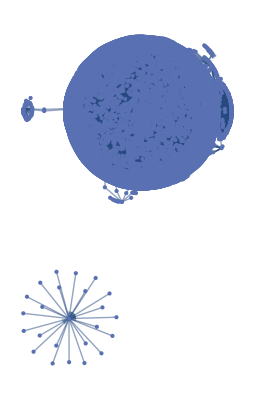

```mathematica
Graph[Flatten@Map[Thread,Normal@Normal@ncDataset[;;,"LinksList"]]]
```